## Define the G-function

```mathematica
carry[v_]:=Kmax*Exp[-v^2/sigmaK^2]
H[v_,m_]:=m*Exp[-v^2/sigmaH^2]
G[v_,u_,x_,m_]:=r*( 1-(x/carry[v]))-H[v,m]
```

## Now, compute the ecological equilibrium x*(u,m)

```mathematica
Solve[G[u,u,x,m]==0,x]
```

{{x→(ⅇ^(-u^2/sigmaH^2-u^2/sigmaK^2) Kmax (-m+ⅇ^(u^2/sigmaH^2) r))/r}}

```mathematica
xstar[u_,m_]:=(ⅇ^(-u^2/sigmaH^2-u^2/sigmaK^2) Kmax (-m+ⅇ^(u^2/sigmaH^2) r))/r
```

## Next, compute evolutionary equilibrium u*(m)

```mathematica
dGdv[v_,u_,x_,m_]:=D[G[v,u,x,m],v]
Simplify[dGdv[v,u,x,m]]
```

(2 ⅇ^(-v^2/sigmaH^2) m v)/sigmaH^2-(2 ⅇ^(v^2/sigmaK^2) r v x)/(Kmax sigmaK^2)

```mathematica
dGdv2[u_,m_]:=dGdv[u,u,xstar[u,m],m]
Simplify[dGdv2[u,m]]
```

0

```mathematica
Simplify[(2 ⅇ^(-u^2/sigmaH^2) m u)/sigmaH^2-(2 ⅇ^(u^2/sigmaK^2) r u)/(Kmax sigmaK^2)(ⅇ^(-u^2/sigmaH^2-u^2/sigmaK^2) Kmax (-m+ⅇ^(u^2/sigmaH^2) r))/r]
```

(2 (-r+ⅇ^(-u^2/sigmaH^2) (m+(m sigmaK^2)/sigmaH^2)) u)/sigmaK^2

```mathematica
Solve[(2 (-r+ⅇ^(-u^2/sigmaH^2) (m+(m sigmaK^2)/sigmaH^2)) u)/sigmaK^2==0,u]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{u→0},{u→-sigmaH √Log[(m sigmaH^2+m sigmaK^2)/(r sigmaH^2)]},{u→sigmaH √Log[(m sigmaH^2+m sigmaK^2)/(r sigmaH^2)]}}

```mathematica
ustar1[m_]:= sigmaH √Log[(m sigmaH^2+m sigmaK^2)/(r sigmaH^2)]
ustar2[m_]:= -sigmaH √Log[(m sigmaH^2+m sigmaK^2)/(r sigmaH^2)]
ustar0[m_]:=0
```

## Test stability of the equilibria

```mathematica
d2Gdv2[v_,u_,x_,m_]:=D[dGdv[v,u,x,m],v]
Simplify[d2Gdv2[v,u,x,m]]
```

-(2 ⅇ^(v^2/sigmaK^2) r (sigmaK^2+2 v^2) x)/(Kmax sigmaK^4)

```mathematica
d2Gdv2[0,0,5,1]
```

General::ivar: 0 is not a valid variable.

∂_0 ∂_0 (-1+(1-5/Kmax) r)

```mathematica
sigmaH=2.0
sigmaK=3.0
r=2.0
```

2.

3.

2.

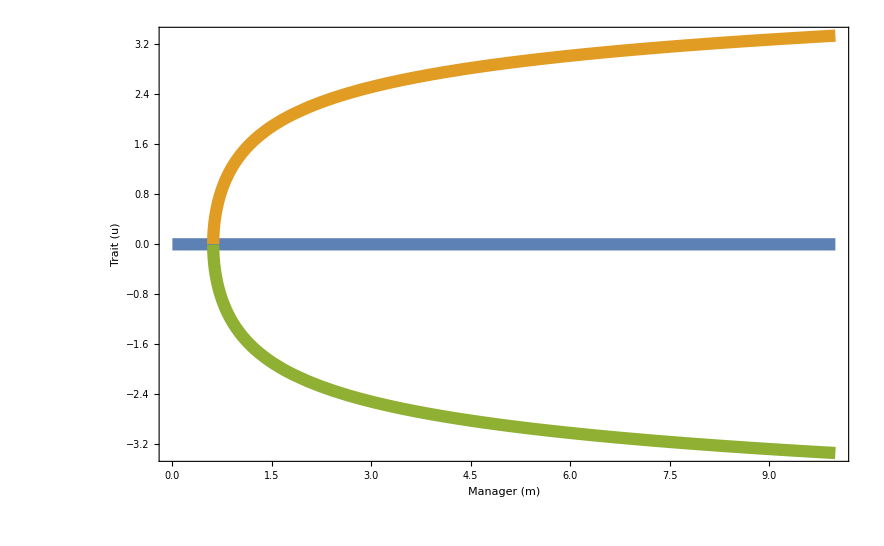

```mathematica
Plot[{ustar0[m],ustar1[m],ustar2[m]},{m,0,10},Frame->True,FrameLabel->{"Manager (m)","Trait (u)"},LabelStyle->"Subtitle",PlotStyle->Thickness[0.01]]
```